
```mathematica
FullForm[-Graphics-]
```

Graphics[Circle[List[0,0]]]

```mathematica
InputForm[-Graphics-]
```

Graphics[Circle[{0, 0}]]

```mathematica
Normal[-Graphics-]
```

```mathematica
Cases[{99,x,y,z,101,102},n_Integer->{n,n}]
```

{{99,99},{101,101},{102,102}}

```mathematica
Function[Power[3,2]][6]
```

9

```mathematica
Function[Power[Slot[2],2]][6,4]
```

16

```mathematica
Select[#>4&][{1,2,4,5}]
```

{5}

```mathematica
Max[1,2]
```

2

```mathematica
Max[#,2]&[4]
```

4

```mathematica
Plus@@{1,2,3,4}
```

10

```mathematica
Plus@@@{{1,2},{3,4}}
```

{3,7}

```mathematica
Tuples[{a,b},2]
```

{{a,a},{a,b},{b,a},{b,b}}

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

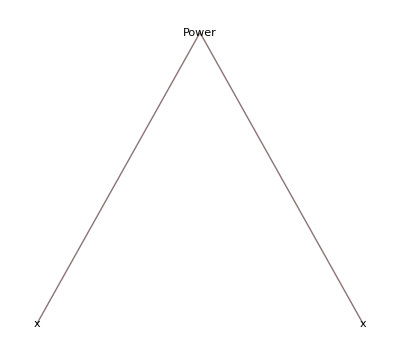
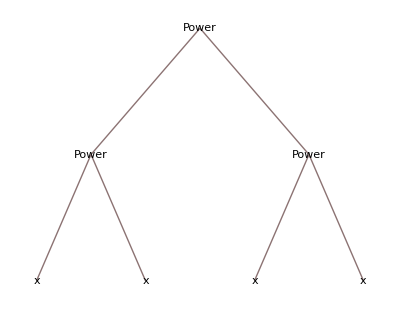
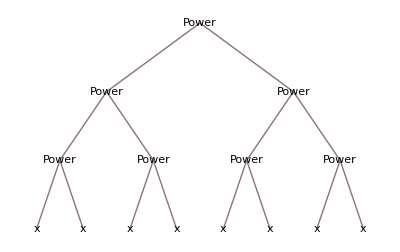
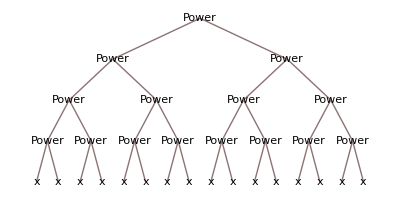
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeForm/@NestList[#^#&,x,4]
```

```mathematica
Select[Flatten@Table[i^2/(j^2+1),{i,20},{j,20}],IntegerQ]//Union
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

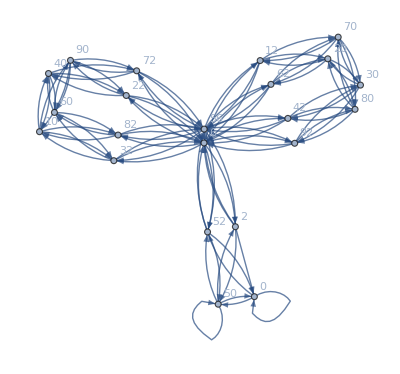

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1],VertexLabels->All]
```

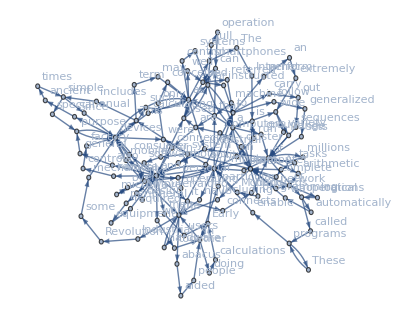

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["computers"],200],2,1],VertexLabels->All]
```

```mathematica
f@@#&/@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

```mathematica
Counts[{a,a,b,c,d,a,c,d,a}]
```

<|12→4,b→1,c→2,d→2|>

```mathematica
#a&@Counts[ToString/@{a,a,b,c,d,a,c,d,a}]
```

4

```mathematica
#e&@LetterCounts[WikipediaData["computers"]]
```

5477

```mathematica
LetterCounts[WikipediaData["computers"]]
```

<|e→5477,t→4019,a→3575,o→3472,r→3281,i→3234,n→3127,s→2834,c→2081,l→1917,m→1662,h→1640,d→1554,u→1521,p→1302,g→916,f→848,y→692,b→611,w→520,v→441,k→212,T→180,C→135,A→127,I→125,M→120,S→116,x→93,P→86,O→69,q→62,U→58,E→58,B→54,R→54,H→48,D→45,L→41,z→41,N→39,F→35,W→35,j→29,J→22,K→20,G→20,Z→10,V→10,ī→4,ū→4,Q→2,ā→2,X→1,â→1,é→1,Y→1|>

```mathematica
a=12
```

12

```mathematica
Values[KeySort[Counts[IntegerDigits[3^100]]]]
```

{7,9,9,5,1,5,4,7,1}

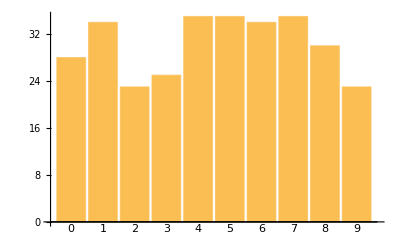

```mathematica
BarChart[KeySort[Counts[IntegerDigits[2^1000]]],ChartLabels->Automatic]
```

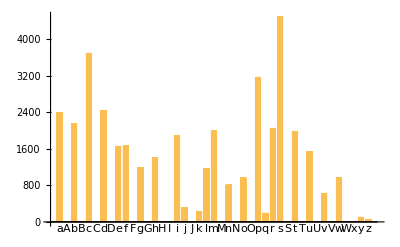

```mathematica
BarChart[Counts[StringTake[#,1]&/@WordList[]],ChartLabels->Automatic]
```

```mathematica
#q/#u&@LetterCounts[WikipediaData["computers"]]//N
```

0.0407627

```mathematica
Keys[TakeLargest[Counts@TextWords[ExampleData[{"Text","AliceInWonderland"}]],10]]
```

{the,and,a,to,she,of,was,Alice,in,it}

```mathematica
Interpreter["Color"]["pink red"]
```

Failure[…]

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
TextStructure["You can do so much with the Wolfram Language.","ConstituentGraphs"]
```

{-Graphics-}

```mathematica
Interpreter["Chemical"]/@{"C2H4","C2H6","C3H8"}
```

{ethylene,ethane,propane}

```mathematica
"U of "<>#&/@ToUpperCase[Alphabet[]]
```

{U of A,U of B,U of C,U of D,U of E,U of F,U of G,U of H,U of I,U of J,U of K,U of L,U of M,U of N,U of O,U of P,U of Q,U of R,U of S,U of T,U of U,U of V,U of W,U of X,U of Y,U of Z}

```mathematica
CommonName/@LinguisticAssistant
```

```mathematica
Cases[Interpreter["City"][StringJoin/@Permutations[{"a","i","l","m"}]],_Entity]
```

{Ilam,Lima,Mali,Milah}

{ailm,aiml,alim,almi,amil,amli,ialm,iaml,ilam,ilma,imal,imla,laim,lami,liam,lima,lmai,lmia,mail,mali,mial,mila,mlai,mlia}

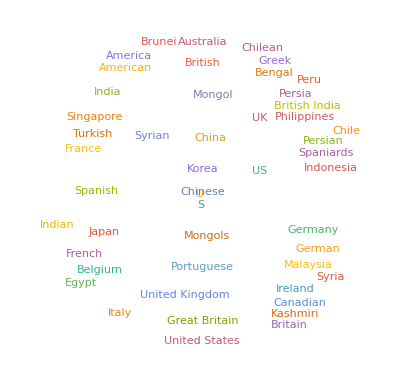

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
```

```mathematica
Length@TextCases[StringTake[WikipediaData["computers"],1000],"Noun"]
```

53

```mathematica
Keys@TakeLargest[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]],10]
```

{door,Rabbit,voice,Mouse,time,way,moment,thing,head,garden}

```mathematica
CommunityGraphPlot[First[TextStructure[First[TextSentences[WikipediaData["language"]]],"ConstituentGraphs"]]]
```

-Graphics-

```mathematica
Length@Flatten[TextCases[WordList[],#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{22728,5894,7146,2824}

```mathematica
WordTranslation[IntegerName@#,"French"]&/@Range[2,10]
```

{{deux},{trois},{quatre},{cinq},{six},{sept},{huit},{neuf},{dix}}